```mathematica
(*Algunas funciones de optimización en Mathematica*)

FindMinimum[x  Cos[x],{x,2}]
```

{-3.28837,{x→3.42562}}

```mathematica
{-3.2883713955908966,{x->3.425618459492147}}
```

{-3.28837,{x→3.42562}}

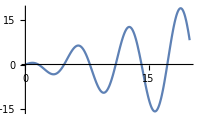

```mathematica
Plot[x  Cos[x],{x,0,20}]
```

```mathematica
x/.Last[FindMinimum[x Cos[x],{x,2}]]
```

3.42562

```mathematica
FindMinimum[{x Cos[x],1≤x≤15},{x,7}]
```

{-9.47729,{x→9.52933}}

```mathematica
FindMinimum[{x+y,x+2 y≥3&&x≥0&&y≥0&&y∈Integers},{x,y}]
```

{2.,{x→0.,y→2}}

```mathematica
FindMinimum[{x+y,{x,y}∈Disk[]},{x,y}]
```

{-1.41422,{x→-0.707108,y→-0.707108}}

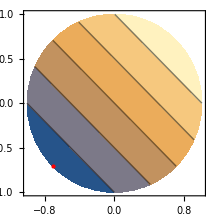

```mathematica
FindMinimum[{x+y,{x,y}∈Disk[]},{x,y}];
Show[ContourPlot[x+y,{x,y}∈Disk[]],Graphics[{Red,PointSize[Large],Point[{x,y}/.Last[%]]}]]
```

```mathematica
LinearProgramming[{1.,1},{{1,1},{1,1}},{{1,-1},{2,1}},Method->"InteriorPoint"]
```

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{1.,1},{{1,1},{1,1}},{{1,-1},{2,1}},Method→InteriorPoint]

```mathematica
Minimize[{x+2 y,-5 x+y==7&&x+y≥26&&x≥3&&y≥4},{x,y}]
```

{293/6,{x→19/6,y→137/6}}

```mathematica
NMinimize[{x+2 y,-5 x+y==7&&x+y≥26&&x≥3&&y≥4},{x,y}]
```

{48.8333,{x→3.16667,y→22.8333}}

```mathematica
LinearProgramming[{1,2},{{-5,1},{1,1}},{{7,0},{26,1}},{{3,Infinity},{4,Infinity}}]
```

{19/6,137/6}

```mathematica
Minimize[{x1+2 x2,-5 x1+x2==7&&x1+x2≥26&&x1≥3&&x2≥4},{x1,x2}]
```

{293/6,{x1→19/6,x2→137/6}}

```mathematica
Minimize[{1400x1+3500x2+2100x3,x1≥0 && x2≥0 &&x3≥0 &&35x1+0.5x2+0.5x3≥0.5   &&  60x1+300x2+10x3≥1 &&  30x1+20x2+10x3≥4 },{x1,x2,x3}]
```

{186.667,{x1→0.133333,x2→0.,x3→0.}}

```mathematica
(*integer-programming*)

SeedRandom[1];
A=Table[RandomInteger[{-1000,1000}],{3},{7}];
α=Table[RandomInteger[{-1000,1000}],{3}];
B=Table[RandomInteger[{-1000,1000}],{3},{7}];
β=Table[RandomInteger[{-1000,1000}],{3}];
γ=Table[RandomInteger[{-1000,1000}],{7}];
X=x/@Range[7];
eqns=And@@Thread[A.X==α];
ineqs=And@@Thread[B.X≤β];
bds=And@@Thread[X≥0]&&Total[X]≤10^100;
Minimize[{γ.X,eqns&&ineqs&&bds&&X∈Integers},X]
```

```mathematica
{448932,{x[1]->990,x[2]->1205,x[3]->219,x[4]->60,x[5]->823,x[6]->137,x[7]->34}}

RegionPlot[γ.X,eqns&&ineqs, bds]

NMinimize[{(x-1/3)^2+(y-1/3)^2,x∈Integers},{x,y}]
```

{448932,{x[1]→990,x[2]→1205,x[3]→219,x[4]→60,x[5]→823,x[6]→137,x[7]→34}}

RegionPlot::pllim: Range specification 674 x[1]-972 x[2]-984 x[3]+551 x[4]+696 x[5]+825 x[6]+21 x[7]==111&&567 x[1]-863 x[2]+202 x[3]+84 x[4]+538 x[5]-195 x[6]+363 x[7]==-906&&120 x[1]-683 x[2]+786 x[3]+216 x[4]+622 x[5]-12 x[6]+258 x[7]==-87&&-894 x[1]-739 x[2]-35 x[3]-111 x[4]+221 x[5]-166 x[6]+429 x[7]≤97&&396 x[1]+171 x[2]-764 x[3]+438 x[4]-722 x[5]+544 x[6]+441 x[7]≤-115&&196 x[1]-833 x[2]+162 x[3]-701 x[4]+398 x[5]-150 x[6]-489 x[7]≤-946 is not of the form {x, xmin, xmax}.

```mathematica
RegionPlot[γ.X,eqns&&ineqs,bds]
```

RegionPlot::pllim: Range specification 674 x[1]-972 x[2]-984 x[3]+551 x[4]+696 x[5]+825 x[6]+21 x[7]==111&&567 x[1]-863 x[2]+202 x[3]+84 x[4]+538 x[5]-195 x[6]+363 x[7]==-906&&120 x[1]-683 x[2]+786 x[3]+216 x[4]+622 x[5]-12 x[6]+258 x[7]==-87&&-894 x[1]-739 x[2]-35 x[3]-111 x[4]+221 x[5]-166 x[6]+429 x[7]≤97&&396 x[1]+171 x[2]-764 x[3]+438 x[4]-722 x[5]+544 x[6]+441 x[7]≤-115&&196 x[1]-833 x[2]+162 x[3]-701 x[4]+398 x[5]-150 x[6]-489 x[7]≤-946 is not of the form {x, xmin, xmax}.

RegionPlot[γ.X,eqns&&ineqs,bds]

```mathematica
NMinimize[{(x-1/3)^2+(y-1/3)^2,x∈Integers},{x,y}]
```

```mathematica
{0.1111111111111111,{x->0,y->0.3333333333333333}}

RegionPlot[(x-1/3)^2+(y-1/3)^2,{x,-200,200},{y,-200,200}]
```

{0.111111,{x→0,y→0.333333}}

ImplicitRegion::bcond: (-1/3+x)^2+(-1/3+y)^2 should be a Boolean combination of equations, inequalities, and Element statements.

-Graphics-

```mathematica
input={{1,4,4},{1,5,9},{1,8,5},{2,1,6},{2,5,3},{3,1,4},{3,2,5},{3,4,6},{3,5,2},{3,7,3},{3,9,7},{4,1,5},{4,3,2},{4,4,7},{4,7,9},{4,8,8},{5,1,3},{5,3,6},{5,7,2},{5,9,1},{6,2,9},{6,3,1},{6,6,2},{6,7,6},{6,9,5},{7,1,2},{7,3,5},{7,5,1},{7,6,4},{7,8,3},{7,9,8},{8,5,8},{8,9,9},{9,2,1},{9,5,7},{9,6,3}};
```

```mathematica
viewmat=Table["",{9},{9}];
Do[viewmat[[input[[i,1]],input[[i,2]]]]=ToString[input[[i,3]]],{i,Length[input]}]
Grid[viewmat,Frame->All]
```

|  |  | 4 | 9 |  |  | 5 | 
6 |  |  |  | 3 |  |  |  | 
4 | 5 |  | 6 | 2 |  | 3 |  | 7
5 |  | 2 | 7 |  |  | 9 | 8 | 
3 |  | 6 |  |  |  | 2 |  | 1
 | 9 | 1 |  |  | 2 | 6 |  | 5
2 |  | 5 |  | 1 | 4 |  | 3 | 8
 |  |  |  | 8 |  |  |  | 9
 | 1 |  |  | 7 | 3 |  |  |

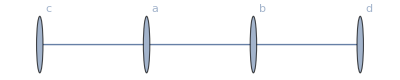

```mathematica
Graph[{a->b,b->da->c},DirectedEdges->False, VertexLabels->"Name"]
```

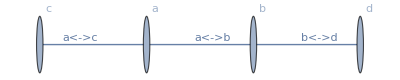

```mathematica
Show[SetProperty[Graph[{a, b, d, c}, {UndirectedEdge[a, b], UndirectedEdge[b, d], UndirectedEdge[a, c]}, {VertexLabels -> {"Name"}}],EdgeLabels->Placed["Name",1./GoldenRatio]],PlotRange->All]
```

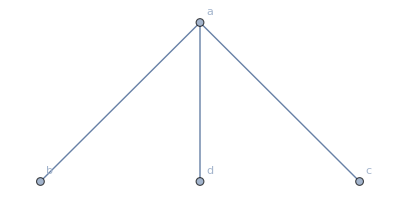

```mathematica
Graph[{a->b,a->d,a->c},DirectedEdges->False, VertexLabels->"Name"]
```

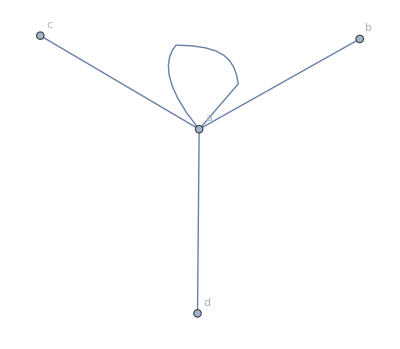

```mathematica
Graph[{a->b,a->d,a->c,a->a},DirectedEdges->False, VertexLabels->"Name"]
```

```mathematica
input={{1,4,4},{1,5,9},{1,8,5},{2,1,6},{2,5,3},{3,1,4},{3,2,5},{3,4,6},{3,5,2},{3,7,3},{3,9,7},{4,1,5},{4,3,2},{4,4,7},{4,7,9},{4,8,8},{5,1,3},{5,3,6},{5,7,2},{5,9,1},{6,2,9},{6,3,1},{6,6,2},{6,7,6},{6,9,5},{7,1,2},{7,3,5},{7,5,1},{7,6,4},{7,8,3},{7,9,8},{8,5,8},{8,9,9},{9,2,1},{9,5,7},{9,6,3}};
```

```mathematica
viewmat=Table["",{9},{9}];
Do[viewmat[[input[[i,1]],input[[i,2]]]]=ToString[input[[i,3]]],{i,Length[input]}]
Grid[viewmat,Frame->All]
```

|  |  | 4 | 9 |  |  | 5 | 
6 |  |  |  | 3 |  |  |  | 
4 | 5 |  | 6 | 2 |  | 3 |  | 7
5 |  | 2 | 7 |  |  | 9 | 8 | 
3 |  | 6 |  |  |  | 2 |  | 1
 | 9 | 1 |  |  | 2 | 6 |  | 5
2 |  | 5 |  | 1 | 4 |  | 3 | 8
 |  |  |  | 8 |  |  |  | 9
 | 1 |  |  | 7 | 3 |  |  |

```mathematica
varmat=Table[m[i,j,k],{i,9},{j,9},{k,9}];
```

```mathematica
vars=Flatten[varmat];
```

```mathematica
cons1=(varmat[[Sequence@@#]]==1&)/@input
```

```mathematica
{m[1,4,4]==1,m[1,5,9]==1,m[1,8,5]==1,m[2,1,6]==1,m[2,5,3]==1,m[3,1,4]==1,m[3,2,5]==1,m[3,4,6]==1,m[3,5,2]==1,m[3,7,3]==1,m[3,9,7]==1,m[4,1,5]==1,m[4,3,2]==1,m[4,4,7]==1,m[4,7,9]==1,m[4,8,8]==1,m[5,1,3]==1,m[5,3,6]==1,m[5,7,2]==1,m[5,9,1]==1,m[6,2,9]==1,m[6,3,1]==1,m[6,6,2]==1,m[6,7,6]==1,m[6,9,5]==1,m[7,1,2]==1,m[7,3,5]==1,m[7,5,1]==1,m[7,6,4]==1,m[7,8,3]==1,m[7,9,8]==1,m[8,5,8]==1,m[8,9,9]==1,m[9,2,1]==1,m[9,5,7]==1,m[9,6,3]==1}
```

```mathematica
cons2=Flatten@Table[(Sum[varmat[[i,j,k]],{k,9}]==1),{i,9},{j,9}];
```

```mathematica
cons3=Flatten@Table[(Sum[varmat[[i,j,k]],{i,9}]==1),{j,9},{k,9}];
```

```mathematica
cons4=Flatten@Table[(Sum[varmat[[i,j,k]],{j,9}]==1),{i,9},{k,9}];
```

```mathematica
sm[di_,dj_]:=Flatten[Table[{i,j},{i,1+3*(di-1),3*di},{j,1+3*(dj-1),3*dj}],1]
cons5=Flatten@Table[(Total[m[Sequence@@#,k]&/@sm[i,j]]==1),{i,3},{j,3},{k,9}];
```

```mathematica
cons6=Thread[0≤vars≤1];
```

```mathematica
Length[allcons=Join[cons1,cons2,cons3,cons4,cons5,cons6]]
```

1089

```mathematica
AbsoluteTiming[sol=FindMinimum[{0,allcons,Element[vars,Integers]},vars];]
```

{0.092408,Null}

```mathematica
resmat=Table[Sum[k*m[i,j,k],{k,9}],{i,9},{j,9}]/.sol[[2]]
```

{{1,2,3,4,9,7,8,5,6},{6,8,7,1,3,5,4,9,2},{4,5,9,6,2,8,3,1,7},{5,4,2,7,6,1,9,8,3},{3,7,6,8,5,9,2,4,1},{8,9,1,3,4,2,6,7,5},{2,6,5,9,1,4,7,3,8},{7,3,4,5,8,6,1,2,9},{9,1,8,2,7,3,5,6,4}}

```mathematica
{Grid[viewmat,Frame->All],Grid[resmat,Frame->All]}
```

{ |  |  | 4 | 9 |  |  | 5 | 
6 |  |  |  | 3 |  |  |  | 
4 | 5 |  | 6 | 2 |  | 3 |  | 7
5 |  | 2 | 7 |  |  | 9 | 8 | 
3 |  | 6 |  |  |  | 2 |  | 1
 | 9 | 1 |  |  | 2 | 6 |  | 5
2 |  | 5 |  | 1 | 4 |  | 3 | 8
 |  |  |  | 8 |  |  |  | 9
 | 1 |  |  | 7 | 3 |  |  | ,1 | 2 | 3 | 4 | 9 | 7 | 8 | 5 | 6
6 | 8 | 7 | 1 | 3 | 5 | 4 | 9 | 2
4 | 5 | 9 | 6 | 2 | 8 | 3 | 1 | 7
5 | 4 | 2 | 7 | 6 | 1 | 9 | 8 | 3
3 | 7 | 6 | 8 | 5 | 9 | 2 | 4 | 1
8 | 9 | 1 | 3 | 4 | 2 | 6 | 7 | 5
2 | 6 | 5 | 9 | 1 | 4 | 7 | 3 | 8
7 | 3 | 4 | 5 | 8 | 6 | 1 | 2 | 9
9 | 1 | 8 | 2 | 7 | 3 | 5 | 6 | 4}

```mathematica
And@@Table[Unequal[Sequence@@resmat[[i]]],{i,9}]
```

True

```mathematica
And@@Table[Unequal[Sequence@@Transpose[resmat][[i]]],{i,9}]
```

True

```mathematica
And@@Flatten@Table[Unequal[resmat[[Sequence@@#]]&/@sm[i,j]],{i,3},{j,3}]
```

True

```mathematica
dataset = Import["/Users/jscs/Downloads/diet.csv","Dataset","HeaderLines"->1]
```

Dataset[<>]

```mathematica
foods = dataset[All,"Foods"]
price = dataset[All,"Price/ Serving"]
calories = dataset[All,"Calories"]
fat = dataset[All,"Total_Fat g"]
sodium =dataset[All,"Sodium mg"]
carbo = dataset[All,"Carbohydrates g"]
protein = dataset[All,"Protein g"]
```

Dataset[<>]

Dataset[<>]

Dataset[<>]

«5 more identical outputs»

```mathematica
nutrients={calories,fat,sodium,carbo,protein}
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

```mathematica
constraints  = {{800,1300},{40,100},{500,2000},{130,450},{60,100}}
```

{{800,1300},{40,100},{500,2000},{130,450},{60,100}}

```mathematica
LinearProgramming[price,nutrients, constraints]
```

LinearProgramming::lprank1: Dataset[«67»] is not a vector.

LinearProgramming[Dataset[<>],{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]},{{800,1300},{40,100},{500,2000},{130,450},{60,100}}]

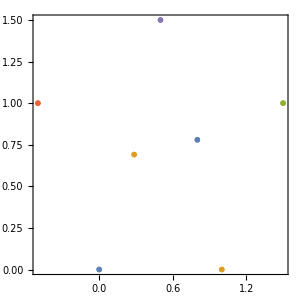
```mathematica
(*Knapsack*)

fruits=<|Entity["FoodType","Apple"]->{Quantity[91,"LargeCalories"],Quantity[2.36,"Euros"],3},Entity["FoodType","Orange"]->{Quantity[71,"LargeCalories"],Quantity[2.12,"Euros"],3},Entity["FoodType","Banana"]->{Quantity[105,"LargeCalories"],Quantity[1.89,"Euros"],5},Entity["FoodType","Kiwi"]->{Quantity[103,"LargeCalories"],Quantity[3.77,"Euros"],10},Entity["FoodType","Pear"]->{Quantity[96,"LargeCalories"],Quantity[2.87,"Euros"],5}|>;
%5
<|Entity["FoodType","Apple"]->{Quantity[91, "LargeCalories"],Quantity["2.36", "Euros"],3},Entity["FoodType","Orange"]->{Quantity[71, "LargeCalories"],Quantity["2.12", "Euros"],3},Entity["FoodType","Banana"]->{Quantity[105, "LargeCalories"],Quantity["1.89", "Euros"],5},Entity["FoodType","Kiwi"]->{Quantity[103, "LargeCalories"],Quantity["3.77", "Euros"],10},Entity["FoodType","Pear"]->{Quantity[96, "LargeCalories"],Quantity["2.87", "Euros"],5}|>
counts=KnapsackSolve[fruits,Quantity[25,"Euros"]]
<|Entity["FoodType","Apple"]->2,Entity["FoodType","Orange"]->1,Entity["FoodType","Banana"]->5,Entity["FoodType","Kiwi"]->0,Entity["FoodType","Pear"]->3|>
fruits[[All,1]] counts
<|Entity["FoodType","Apple"]->Quantity[182, "LargeCalories"],Entity["FoodType","Orange"]->Quantity[71, "LargeCalories"],Entity["FoodType","Banana"]->Quantity[525, "LargeCalories"],Entity["FoodType","Kiwi"]->Quantity[0, "LargeCalories"],Entity["FoodType","Pear"]->Quantity[288, "LargeCalories"]|>
Total[%]
Quantity[1066, "LargeCalories"]
fruits[[All,2]] counts
<|Entity["FoodType","Apple"]->Quantity["4.72", "Euros"],Entity["FoodType","Orange"]->Quantity["2.12", "Euros"],Entity["FoodType","Banana"]->Quantity["9.45", "Euros"],Entity["FoodType","Kiwi"]->Quantity["0.00", "Euros"],Entity["FoodType","Pear"]->Quantity["8.61", "Euros"]|>

Total[%]
Quantity["24.90", "Euros"]

(*Ubicación*)

totalCost=Total[c d,2];
Total[c d,2]
Total[c d,2]
constraints[n_,m_]:=Table[Norm[p[i]-q[j]]≤Indexed[d,{i,j}],{i,n},{j,m}];
nFactories=2;
nWarehouses=5;
warehousePosition={{0,0},{1,0},{3/2,1},{-1/2,1},{1/2,3/2}};
costPerUnitDistance=({{1000,1500,2000,1000,1500},{1500,1500,1000,2000,1500}});
res=SecondOrderConeOptimization[totalCost,{c==costPerUnitDistance,constraints[nFactories,nWarehouses],Table[q[i]==warehousePosition[[i]],{i,nWarehouses}]},{d,p[1]∈Vectors[2],p[2]∈Vectors[2]}]
{d->{{1.1176086914339836,0.805137851254597,0.7333734526456266,1.3188786997535569,0.7801500668991149},{0.7473848268318596,0.9942528980371386,1.2536791364985407,0.8436835230378843,0.8371703350815509}},p[1]->{0.8004010904196929,0.7800046487975456},p[2]->{0.28502263932427224,0.6909024287256987}}
Show[ListPlot[Thread[{warehousePosition}],Sequence[Axes->False,Frame->True,PlotMarkers->{Style["A\n$1000\n$1500",GrayLevel[0],14],Style["B\n$1500\n$1500",GrayLevel[0],14],Style["C\n$2000\n$1000",GrayLevel[0],14],Style["D\n$1000\n$2000",GrayLevel[0],14],Style["E\n$1500\n$1500",GrayLevel[0],14]},FrameStyle->Bold,PlotRangePadding->1/2,AspectRatio->1,ImageSize->300]],ListPlot[{{p[1]},{p[2]}}/.res,PlotMarkers->Map[Style[#,Red,14]&,{"F1","F2"}]]]
-Graphics-
```

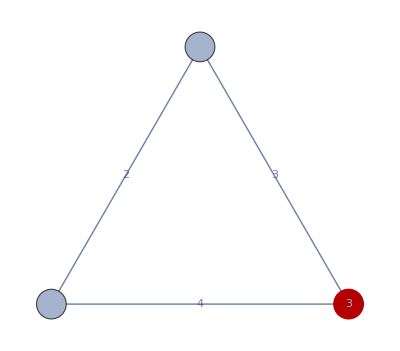
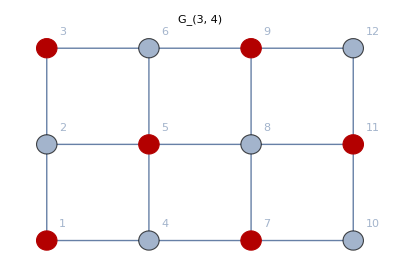
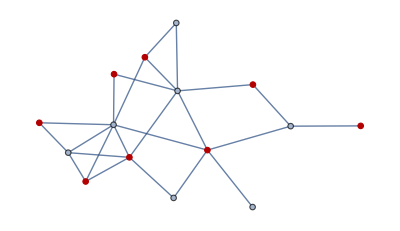
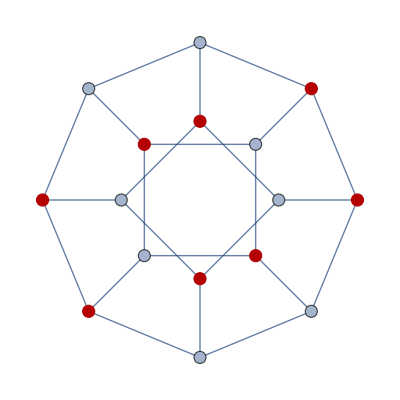
```mathematica
(*Problema de Asignación*)
totalCost=Total[c x,2];
totalProfit=Total[p x,2];
supplyConstraint=Total[x,{2}]\[VectorGreaterEqual]minSupply;
minDemandConstraint=Total[x,1]\[VectorGreaterEqual]minDemand;
peakDemandConstraint=Total[x,1]\[VectorLessEqual]peakDemand;
negativePowerConstraint=x\[VectorGreaterEqual]0;
nPlants=4;
nCities=5;
cost={{8,6,10,9,7},{9,12,13,7,8},{14,9,16,5,6},{8,5,7,8,8}};
GraphicsRow[Table[BarChart[Part[cost,i],LabelingFunction->"RadialCenter",PlotLabel->StringForm["Plant `1` cost",i],ChartLabels->{Subscript[c,1],Subscript[c,2],Subscript[c,3],Subscript[c,4],Subscript[c,5]},ChartElementFunction->"GlassRectangle",ChartStyle->101,BarSpacing->None,ImageSize->130],{i,1,nPlants}]]
-Graphics-
profit={{5,4,4,3,4},{6,2,3,4,5},{10,5,6,2,4},{8,7,5,5,7}};
GraphicsRow[Table[BarChart[Part[profit,i],LabelingFunction->"RadialCenter",PlotLabel->StringForm["Plant `1` profit",i],ChartLabels->{Subscript[c,1],Subscript[c,2],Subscript[c,3],Subscript[c,4],Subscript[c,5]},ChartElementFunction->"GlassRectangle",ChartStyle->101,BarSpacing->None,ImageSize->130],{i,1,nPlants}]]
-Graphics-
minDemand={5,5,5,5,5};
peakDemand={45,20,30,30,40};
minSupply={35,50,40,40};
res=LinearFractionalOptimization[totalCost/totalProfit,{c==cost,p==profit,minDemandConstraint,peakDemandConstraint,supplyConstraint,negativePowerConstraint},x∈Matrices[{nPlants,nCities}]]
{x->{{0,0,10,0,25},{5,0,0,30,15},{40,0,0,0,0},{0,20,20,0,0}}}
TableForm[(x/.res),TableHeadings->{{"Plant 1","Plant 2","Plant 3","Plant 4"},{"City 1","City 2","City 3","City 4","City 5"}}]
{{, "City 1", "City 2", "City 3", "City 4", "City 5"}, {"Plant 1", 0, 0, 10, 0, 25}, {"Plant 2", 5, 0, 0, 30, 15}, {"Plant 3", 40, 0, 0, 0, 0}, {"Plant 4", 0, 20, 20, 0, 0}}

(*Problema del Corte Máximo*)

laplacianMatrix[G_?GraphQ]:=(DiagonalMatrix[Total[#,{1}]]-#)&[WeightedAdjacencyMatrix[G]]

maxCutExact[G_?GraphQ]:=Module[{L=laplacianMatrix[G],n,x},n=Length[First[L]];
x=Array["var",n];
MaxValue[{1/4 x.L.x,x^2==ConstantArray[1,n]},x,Integers]]
e[i_,n_]:=SparseArray[{i,i}->1.,{n,n},0.];
maxCutRelaxed[G_?GraphQ,trials_: 10]:=Module[{L=laplacianMatrix[G],Y,U,n,sdpmax,x},n=Length[First[L]];{Y,sdpmax}=SemidefiniteOptimization[ConstantArray[1,n],Join[{-L/4},Table[e[i,n],{i,n}]],{"DualMaximizer","DualMaximumValue"}];
U=CholeskyDecomposition[Y];
x=First[MaximalBy[Table[Sign[RandomPoint[Sphere[n]].U],trials],1/4 #.L.#&]];
{sdpmax,1/4 x.L.x,HighlightGraph[G,Pick[Range[n],x,1]]}]
triang=Graph[{1<->2,2<->3,3<->1},EdgeWeight->{2,3,4},VertexSize->Small,VertexLabels->Placed["Name",Center],EdgeLabels->"EdgeWeight"];
{maxCutExact[triang],maxCutRelaxed[triang]}
{7,{7.041666629402523,7,-Graphics-}}
grid=GridGraph[{3,4},PlotLabel->"\!\(\*SubscriptBox[\(G\), \(3, 4\)]\)",VertexLabels->"Name",VertexSize->Medium];
{maxCutExact[grid],maxCutRelaxed[grid]}
{17,{16.99999996370457,17,-Graphics-}}
g1=RandomGraph[{15,24}];
{maxCutExact[g1],maxCutRelaxed[g1]}
{21,{21.16093225435047,21,-Graphics-}}
pet=PetersenGraph[8,2,VertexSize->Medium];
AbsoluteTiming[maxCutExact[pet]]
{3.003197,20}
AbsoluteTiming[maxCutRelaxed[pet]]
{0.006355,{21.348469204338144,20,-Graphics-}}
```

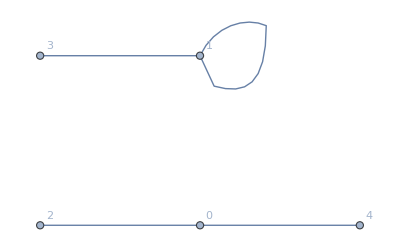
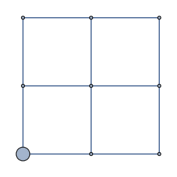
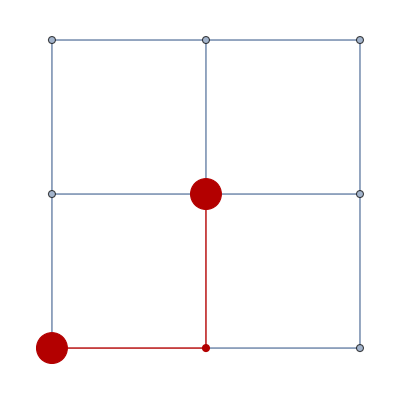
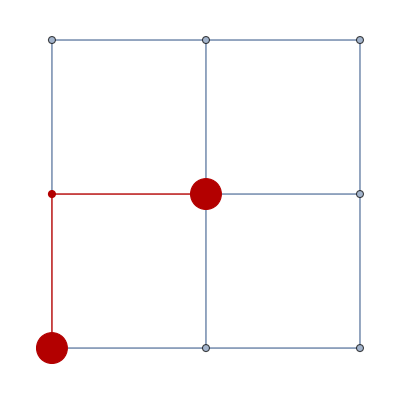
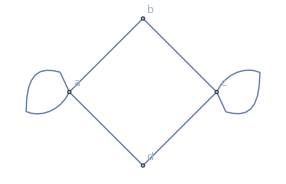
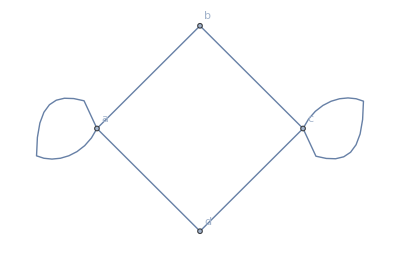
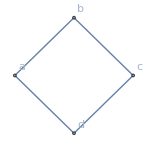
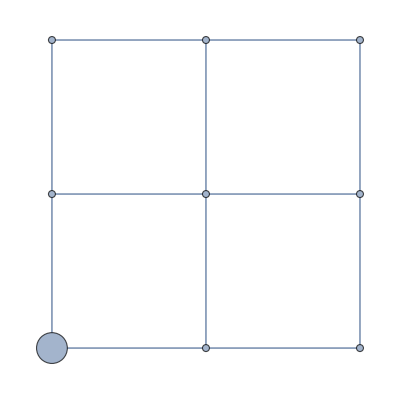
```mathematica
(*Construir un grafo*)
l=Table[i<->Mod[i,2],{i,4}]
{1<->1,2<->0,3<->1,4<->0}
Graph[l,VertexLabels->"Name"]
-Graphics-

(*Caminos*)
s=1;
t=5;
g=GridGraph[{3,3},VertexSize->{s->Medium}]
-Graphics-
FindPath[g,s,t,2,All]
{{1,4,5},{1,2,5}}
HighlightGraph[g,PathGraph[#]]&/@%
{-Graphics-,-Graphics-}
Graph[{a<->b,b<->c,c<->d,a<->d,a<->a,c<->c}, VertexLabels->"Name"]
-Graphics-

SimpleGraph[-Graphics-]
-Graphics-


(*Ciclos*)
g=-Graphics-;
FindCycle[{g,1}]
{{1<->2,2<->5,5<->8,8<->7,7<->4,4<->1}}
Table[HighlightGraph[g,Part[First[%],1;;i]],{i,Length[First[%]]}]
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(*Caminos Eulerianos*)
FindEulerianCycle[-Graphics-]
{}
g=Graph[GraphData["ButterflyGraph"],VertexLabels->"Name"]
-Graphics-

FindEulerianCycle[GraphData["ButterflyGraph"]]
{{1<->5,5<->4,4<->1,1<->3,3<->2,2<->1}}
Table[HighlightGraph[g,Part[First[%],1;;i]],{i,Length[First[%]]}]
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(*Grafos conectados*)
ConnectedGraphQ[-Graphics-]
False

(*Konigsberg*)
l=List[A<->B,B<->D,D<->C,C<->A,A<->C,D<->C,B<->C];
g=Graph[l,VertexLabels->"Name"]
-Graphics-
FindEulerianCycle[g]
{}

(*Grafos dirigidos*)
g=DirectedGraph[-Graphics-,"Random"]
-Graphics-


FindPath[g,A,D]
{}
HighlightGraph[g,List[A->C,C->B,B->D]]
-Graphics-
FindPath[g,B,D]
{}
(*Grafos con pesos*)
s=SparseArray[{{1,2}->10,{2,1}->10,{1,3}->z,{3,1}->z,
{2,3}->2/3,{3,2}->2/3},{3,3},Infinity];
MatrixForm[s]
({{∞, 10, z}, {10, ∞, 2/3}, {z, 2/3, ∞}})

WeightedAdjacencyGraph[s,VertexLabels->"Name" ,EdgeLabels->"EdgeWeight"]
-Graphics-

d=SparseArray[{{1,2}->100,{1,3}->100,{1,4}->150,{2,3}->150,
{2,4}->100,{3,4}->100,{3,5}->150,{4,5}->150,{2,1}->100,
{3,1}->100,{4,1}->150,{3,2}->150,{4,2}->100,{4,3}->100,
{5,3}->150,{5,4}->150},{5,5},Infinity];
MatrixForm[d]
({{∞, 100, 100, 150, ∞}, {100, ∞, 150, 100, ∞}, {100, 150, ∞, 100, 150}, {150, 100, 100, ∞, 150}, {∞, ∞, 150, 150, ∞}})
HighlightGraph[WeightedAdjacencyGraph[d,GraphStyle->"SmallNetwork",
EdgeLabels->"EdgeWeight"],{1<->4,4<->3,3<->5}]
-Graphics-

(*Arboles*)

g=TreeGraph[RandomInteger[#]<->#+1&/@Range[0,10],VertexLabels->"Name"]


-Graphics-

(*Minimum Spanning Tree*)
SparseArray[{{1,2}->10,{2,3}->12,{2,4}->15,{3,4}->5,{4,5}->15,
{1,5}->25,{2,1}->10,{3,2}->12,{4,2}->15,{4,3}->5,{5,4}->15,
{5,1}->25},{5,5},Infinity];
g=WeightedAdjacencyGraph[%,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]
-Graphics-
suficiente={4<->3,3<->2};
HighlightGraph[g,%]
-Graphics-
innecesario={4<->3,3<->2,2<->4};
HighlightGraph[g,%]
-Graphics-
l={4<->3,1<->2,2<->3,5<->4};
Table[HighlightGraph[g,Part[Out[7],1;;i]],{i,4}]
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
l={4<->3,3<->2,2<->1,4<->5};
Table[HighlightGraph[g,Part[Out[9],1;;i]],{i,4}]
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
ciudades={"Monteria","Necocli","Cartagena","Barranquilla","Soledad","Santa Marta","Medellin","Ayapel"};
coordinates=CityData[#,"Coordinates"]&/@%
{{8.76,-75.89},{8.43,-76.79},{10.4,-75.5},{10.96,-74.8},{10.92,-74.77},{11.26,-74.19},{6.29,-75.54},{8.33,-75.15}}
distances=Flatten[Table[EuclideanDistance[Part[Out[12],i],Part[Out[12],j]],{i,7},{j,i+1,8}]]
{0.9585927185202328,1.6857342613828559,2.45521893117498,2.4331050121192903,3.0232432915661964,2.4946743274423606,0.85586213843118,2.3547823678633275,3.218850726579293,3.2063218802858895,3.843032656639811,2.4783260479605986,1.6430459518832703,0.8964373932406013,0.8962700485902703,1.5670673246545614,4.110194642592976,2.0993808611111984,0.05000000000000142,0.6797793759742926,4.728266066963663,2.65318676312091,0.6723094525588629,4.693591375482106,2.6177280225416864,5.150087377899527,3.083261260418911,2.0769448716805172}
Flatten[Table[{i,j},{i,7},{j,i+1,8}],1];
Flatten[Table[{j,i},{i,7},{j,i+1,8}],1];
Table[Part[Out[18],i]->Part[Out[16],i],{i,28}];
Table[Part[Out[19],i]->Part[Out[16],i],{i,28}];
lista=Flatten[List[Out[20],Out[22]],1]
{{1,2}->0.9585927185202328,{1,3}->1.6857342613828559,{1,4}->2.45521893117498,{1,5}->2.4331050121192903,{1,6}->3.0232432915661964,{1,7}->2.4946743274423606,{1,8}->0.85586213843118,{2,3}->2.3547823678633275,{2,4}->3.218850726579293,{2,5}->3.2063218802858895,{2,6}->3.843032656639811,{2,7}->2.4783260479605986,{2,8}->1.6430459518832703,{3,4}->0.8964373932406013,{3,5}->0.8962700485902703,{3,6}->1.5670673246545614,{3,7}->4.110194642592976,{3,8}->2.0993808611111984,{4,5}->0.05000000000000142,{4,6}->0.6797793759742926,{4,7}->4.728266066963663,{4,8}->2.65318676312091,{5,6}->0.6723094525588629,{5,7}->4.693591375482106,{5,8}->2.6177280225416864,{6,7}->5.150087377899527,{6,8}->3.083261260418911,{7,8}->2.0769448716805172,{2,1}->0.9585927185202328,{3,1}->1.6857342613828559,{4,1}->2.45521893117498,{5,1}->2.4331050121192903,{6,1}->3.0232432915661964,{7,1}->2.4946743274423606,{8,1}->0.85586213843118,{3,2}->2.3547823678633275,{4,2}->3.218850726579293,{5,2}->3.2063218802858895,{6,2}->3.843032656639811,{7,2}->2.4783260479605986,{8,2}->1.6430459518832703,{4,3}->0.8964373932406013,{5,3}->0.8962700485902703,{6,3}->1.5670673246545614,{7,3}->4.110194642592976,{8,3}->2.0993808611111984,{5,4}->0.05000000000000142,{6,4}->0.6797793759742926,{7,4}->4.728266066963663,{8,4}->2.65318676312091,{6,5}->0.6723094525588629,{7,5}->4.693591375482106,{8,5}->2.6177280225416864,{7,6}->5.150087377899527,{8,6}->3.083261260418911,{8,7}->2.0769448716805172}
s=SparseArray[Flatten[Table[Part[Out[23],i],{i,56}]],{8,8},Infinity];
g=WeightedAdjacencyGraph[s,VertexLabels->{1->"Monteria",2-> "Necocli",3->"Cartagena",
4->"Barranquilla",5->"Soledad",6->"Santa Marta",7->"Medellin",8->"Ayapel"},
EdgeLabels->"EdgeWeight"]
-Graphics-
st=FindSpanningTree[g]
-Graphics-
HighlightGraph[g,st]
-Graphics-

(*Traveling Salesman Problem*)
colombia=CityData[{Large,"Colombia"}]
{Entity["City",{"Bogota","DistritoCapital","Colombia"}],Entity["City",{"Medellin","Antioquia","Colombia"}],Entity["City",{"Cali","ValleDelCauca","Colombia"}],Entity["City",{"Barranquilla","Atlantico","Colombia"}],Entity["City",{"Cartagena","Bolivar","Colombia"}],Entity["City",{"Cucuta","NorteDeSantander","Colombia"}],Entity["City",{"Bucaramanga","Santander","Colombia"}],Entity["City",{"Soledad","Atlantico","Colombia"}],Entity["City",{"Ibague","Tolima","Colombia"}],Entity["City",{"Soacha","Cundinamarca","Colombia"}],Entity["City",{"SantaMarta","Magdalena","Colombia"}],Entity["City",{"Villavicencio","Meta","Colombia"}],Entity["City",{"Pereira","Risaralda","Colombia"}],Entity["City",{"Manizales","Caldas","Colombia"}],Entity["City",{"Bello","Antioquia","Colombia"}],Entity["City",{"Valledupar","Cesar","Colombia"}],Entity["City",{"Pasto","Narino","Colombia"}],Entity["City",{"Buenaventura","ValleDelCauca","Colombia"}],Entity["City",{"Monteria","Cordoba","Colombia"}],Entity["City",{"Neiva","Huila","Colombia"}],Entity["City",{"Itagui","Antioquia","Colombia"}],Entity["City",{"Armenia","Quindio","Colombia"}],Entity["City",{"Floridablanca","Santander","Colombia"}],Entity["City",{"Popayan","Cauca","Colombia"}],Entity["City",{"Palmira","ValleDelCauca","Colombia"}],Entity["City",{"Sincelejo","Sucre","Colombia"}],Entity["City",{"DosQuebradas","Risaralda","Colombia"}],Entity["City",{"Envigado","Antioquia","Colombia"}],Entity["City",{"Barrancabermeja","Santander","Colombia"}],Entity["City",{"Tulua","ValleDelCauca","Colombia"}],Entity["City",{"Tunja","Boyaca","Colombia"}],Entity["City",{"Riohacha","LaGuajira","Colombia"}],Entity["City",{"Maicao","LaGuajira","Colombia"}],Entity["City",{"Girardot","Cundinamarca","Colombia"}],Entity["City",{"Sogamoso","Boyaca","Colombia"}],Entity["City",{"Giron","Santander","Colombia"}],Entity["City",{"Florencia","Caqueta","Colombia"}],Entity["City",{"Apartado","Antioquia","Colombia"}],Entity["City",{"Cartago","ValleDelCauca","Colombia"}],Entity["City",{"Buga","ValleDelCauca","Colombia"}],Entity["City",{"Quibdo","Choco","Colombia"}],Entity["City",{"Facatativa","Cundinamarca","Colombia"}]}
pos=CityData[#,"Coordinates"]&/@colombia;
FindShortestTour[pos]
{33.67458365988145,{1,10,12,31,35,29,23,36,7,6,16,33,32,11,4,8,5,26,19,38,2,15,28,21,41,14,13,27,39,22,30,40,25,3,18,24,17,37,20,9,34,42,1}}
GeoGraphics[{Thick,Red,GeoPath[pos[[Last[%]]]]}]
-Graphics-

(*Clique Cover*)
g=ExampleData[{"NetworkGraph","FamilyGathering"}]
-Graphics-
FindClique[g,6,All]
{{"James","Anna","Linda","Larry","Nancy"},{"Larry","Carol","Ben","Oscar"},{"Linda","Michael","Nora","Julia"},{"Nancy","David","Arlene"},{"John","Dorothy","David"},{"Arlene","Rudy"},{"Oscar","Felicia"},{"Elisabeth","Anna"}}
HighlightGraph[g,Subgraph[g,#]&/@%]
-Graphics-
FindClique[g,7,All]
{{"James","Anna","Linda","Larry","Nancy"},{"Larry","Carol","Ben","Oscar"},{"Linda","Michael","Nora","Julia"},{"Nancy","David","Arlene"},{"John","Dorothy","David"},{"Arlene","Rudy"},{"Oscar","Felicia"},{"Elisabeth","Anna"}}
```